```mathematica
ps[n_,s_]:=n^s/s HarmonicNumber[n,s]-n^(1-s)/(1-s) HarmonicNumber[n,1-s]
ps2[n_,s_]:=n^(s-1)(1-s) HarmonicNumber[n,s]-n^(-s) s  HarmonicNumber[n,1-s]
ps3[n_,s_]:=(1-s)n^(s-1/2) HarmonicNumber[n,s]+s n^(1/2-s) HarmonicNumber[n,1-s]
ps4[n_,x_]:=(1/2+x)n^(-x) HarmonicNumber[n,1/2-x]-(1/2-x) n^x HarmonicNumber[n,1/2+x]
ps5[n_,s_]:=n^(-1/2+s) (1-s) HarmonicNumber[n,s]-n^(1/2-s) s HarmonicNumber[n,1-s]
ps6[n_,s_]:=n^(-1/2+s) (1-s)Zeta[s,n+1]-n^(1/2-s) s Zeta[1-s,n+1]
ps7[n_,s_]:=Sum[ j^(-1/2)((1-2s)Cosh[ (1/2-s)Log[j/n]]+Sinh[(1/2-s)Log[j/n]]),{j,1,n}]
ps8[n_,s_,t_]:=n^(-1/2+s+t) (1-s) HarmonicNumber[n,s]-n^(1/2-s+t) s HarmonicNumber[n,1-s]
```

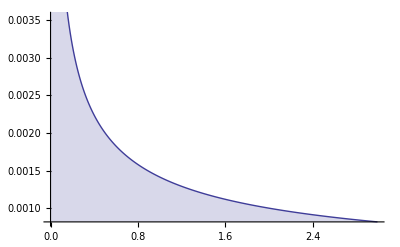

```mathematica
DiscretePlot[{Abs[ps5[n,N@ZetaZero@1]]},{n,1,300000000,1000000}]
```

```mathematica
ps4[n,1/2-x]/.x->s
```

-n^(1/2-s) s HarmonicNumber[n,1-s]+n^(-1/2+s) (1-s) HarmonicNumber[n,s]

```mathematica
FullSimplify[j^(-1/2)( 2(1/2-s)Cosh[ (1/2-s)Log[j/n]]+Sinh[(1/2-s)Log[j/n]])]
```

((1-2 s) Cosh[(1/2-s) Log[j/n]]+Sinh[(1/2-s) Log[j/n]])/(√j)

```mathematica
N@ZetaZero@10
```

0.5+49.7738 ⅈ

```mathematica
Sum[FullSimplify[(1-s)(n/j)^s -s(j/n)^s],{j,1,n}]
```

$Aborted

```mathematica
Abs[ps8[100000000,N@ZetaZero@1,0]]
```

0.00141347

```mathematica
ps8a[n_,s_,t_]:=(n^(-1/2+s+t) (1-s) HarmonicNumber[n,s]-n^(1/2-s+t) s HarmonicNumber[n,1-s])/((1-s)n^(s-1/2+t)-s n^(1/2-s+t)(2^(1-s)Pi^(-s)Cos[Pi s/2]Gamma[s]))
ps8b[n_,s_,t_]:=(n^(-1/2+s+t) (1-s) HarmonicNumber[n,s]-n^(1/2-s+t) s HarmonicNumber[n,1-s])/((1-s)n^(s-1/2+t)-s n^(1/2-s+t)(Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps8c[n_,s_,t_]:={n^(-1/2+s+t) (1-s) HarmonicNumber[n,s],-n^(1/2-s+t) s HarmonicNumber[n,1-s],(1-s)n^(s-1/2+t),-s n^(1/2-s+t)(Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2])}
ps8c2[n_,s_,t_]:={n^(-1/2+s+t) (1-s) HarmonicNumber[n,s]-n^(1/2-s+t) s HarmonicNumber[n,1-s],(1-s)n^(s-1/2+t)-s n^(1/2-s+t)(Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2])}
```

```mathematica
ps8a[10000000,N@ZetaZero@10,0]
```

-0.0000726868+0.000140831 ⅈ

```mathematica
Zeta[.3]
```

-0.904559

```mathematica
ps8c[1000000000,N@ZetaZero@10,0]
```

{31622.8-0.000786999 ⅈ,-31622.8-0.000786999 ⅈ,43.0282-25.0252 ⅈ,45.3245-20.576 ⅈ}

```mathematica
fn[n_,s_,t_]:=n^(1/2+t)/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000)
fna[n_,s_,t_]:=n^(1/2+t)/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600)
fnb[n_,s_,t_]:=n^(1/2+t)/(1/(232792560 (-1+s))n^(-19-s) (456 n^4 (-17 n^2 (715 n^8 Binomial[1-s,6]-1001 n^6 Binomial[1-s,8]+2275 n^4 Binomial[1-s,10]-7601 n^2 Binomial[1-s,12]+35035 Binomial[1-s,14])+3620617 Binomial[1-s,16])-12796881240 n^2 Binomial[1-s,18]+29393 (-11 n^16 (720 n^4-360 n^3 (-1+s)+60 n^2 (-1+s) s-(-1+s) s (1+s) (2+s))+4190664 Binomial[1-s,20])))
fnc[n_,s_,t_]:=n^(1/2+t)/(n^-s/2+n^(1-s)/(1-s))
fnd[n_,s_,t_]:=n^(1/2+t)/(n^(1-s)/(1-s))
```

```mathematica
ps9[n_,s_,t_]:=(fn[n,s,t] HarmonicNumber[n,s]-fn[n,1-s,t] HarmonicNumber[n,1-s])/(fn[n,s,t]-fn[n,1-s,t](Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps9a[n_,s_,t_]:=(fn[n,s,t] HarmonicNumber[n,s]-fn[n,1-s,t] HarmonicNumber[n,1-s])
ps9aa[n_,s_,t_]:=(fna[n,s,t] HarmonicNumber[n,s]-fna[n,1-s,t] HarmonicNumber[n,1-s])
ps9ab[n_,s_,t_]:=(fnb[n,s,t] HarmonicNumber[n,s]-fnb[n,1-s,t] HarmonicNumber[n,1-s])
ps9ac[n_,s_,t_]:=(fnc[n,s,t] HarmonicNumber[n,s]-fnc[n,1-s,t] HarmonicNumber[n,1-s])
ps9ad[n_,s_,t_]:=(fnd[n,s,t] HarmonicNumber[n,s]-fnd[n,1-s,t] HarmonicNumber[n,1-s])
ps9b[n_,s_,t_]:=(fn[n,s,t] HarmonicNumber[n,s])
```

```mathematica
N[ps9a[1000,ZetaZero@10,-.5]]
```

0.-0.279365 ⅈ

```mathematica
N[ps5[100000000,ZetaZero@10]]
```

0.-0.00497738 ⅈ

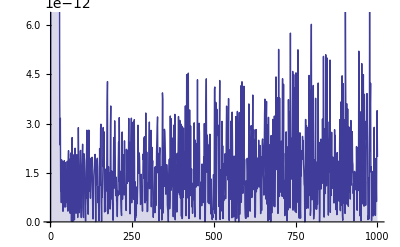

```mathematica
DiscretePlot[ Abs@ps9a[n,N@ZetaZero@10,0],{n,1,1000,1}]
```

```mathematica
Zeta[.5+100000I]
```

1.07303+5.78085 ⅈ

```mathematica
100000^.5
```

316.228

```mathematica
ps10[n_,s_,t_]:=n^(-1/2+s+t)  HarmonicNumber[n,s]-n^(1/2-s+t) HarmonicNumber[n,1-s]
ps11[n_,s_,t_,a_,b_]:=n^(-1/2+s+t) (1-s)^a/s^(1-b) HarmonicNumber[n,s]-n^(1/2-s+t) s^b/(1-s)^(1-a) HarmonicNumber[n,1-s]
ps12[n_,s_,t_,a_,b_]:=n^(-1/2+s+t) (1-s)^a s^(b-1) HarmonicNumber[n,s]-n^(1/2-s+t) s^b (1-s)^(a-1) HarmonicNumber[n,1-s]
```

```mathematica
ps11[1000000000,N@ZetaZero@1+.1I,0,.5,.5]
```

0.-0.0266785 ⅈ

```mathematica
(1-s)^a/s^b /. a->3/.b->2/.s->.35
```

2.24184

```mathematica
((1-s)/s) s^(b-a) /. a->3/.b->2/.s->.35
```

5.30612

```mathematica
(1-s)^a s^-b /. a->3/.b->2/.s->.35
```

2.24184

```mathematica
((1-s)/s)^a  s^(-b+a) /. a->3/.b->2/.s->.35
```

2.24184

```mathematica
(1/s-1)^a  s^(a-b) /. a->3/.b->2/.s->.35
```

2.24184

```mathematica
2Pi^(s/2)/Gamma[s/2]/.s->.3
```

0.381762

```mathematica
2Pi^(s/2)Gamma[1-s/2]Sin[Pi s/2]/Pi/.s->.3
```

0.381762

```mathematica
2Pi^(s/2-1)Gamma[1-s/2]Sin[Pi s/2]/.s->.3
```

0.381762

```mathematica
FullSimplify[2Pi^(s/2-1)Gamma[1-s/2]Sin[Pi s/2]/.s->1-s]
```

2 π^(-1/2-s/2) Cos[(π s)/2] Gamma[(1+s)/2]

```mathematica
2Pi^(s/2-1)Gamma[1-s/2]Sin[Pi s/2]
```

2 π^(-1+s/2) Gamma[1-s/2] Sin[(π s)/2]

```mathematica
N@PolyGamma[2,10]
```

-0.0110498

```mathematica
D[n^(-1/2+s) (1-s) HarmonicNumber[n,s]-n^(1/2-s) s HarmonicNumber[n,1-s],n]
```

-n^(-1/2-s) (1/2-s) s HarmonicNumber[n,1-s]+n^(-3/2+s) (1-s) (-1/2+s) HarmonicNumber[n,s]-n^(1/2-s) (1-s) s (-HarmonicNumber[n,2-s]+Zeta[2-s])+n^(-1/2+s) (1-s) s (-HarmonicNumber[n,1+s]+Zeta[1+s])

```mathematica
fa[n_,s_]:=1/2 n^(-3/2-s) (n s (-1+2 s) HarmonicNumber[n,1-s]+(-1+s) (2 n^2 s HurwitzZeta[2-s,1+n]+n^(2 s) ((1-2 s) HarmonicNumber[n,s]-2 n s HurwitzZeta[1+s,1+n])))
```

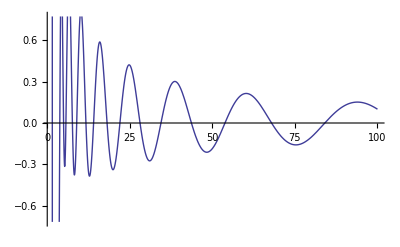

```mathematica
Plot[Im@fa[n,N@ZetaZero@1+.1],{n,1,100}]
```

```mathematica
FullSimplify[-n^(-1/2-s) (1/2-s) s HarmonicNumber[n,1-s]+n^(-3/2+s) (1-s) (-1/2+s) HarmonicNumber[n,s]-n^(1/2-s) (1-s) s (-HarmonicNumber[n,2-s]+Zeta[2-s])+n^(-1/2+s) (1-s) s (-HarmonicNumber[n,1+s]+Zeta[1+s])]
```

1/2 n^(-3/2-s) (n s (-1+2 s) HarmonicNumber[n,1-s]+(-1+s) (2 n^2 s HurwitzZeta[2-s,1+n]+n^(2 s) ((1-2 s) HarmonicNumber[n,s]-2 n s HurwitzZeta[1+s,1+n])))

```mathematica
2Pi^(s/2)/Gamma[s/2]/.s->.3
```

0.381762

```mathematica
2Pi^(s/2)/Gamma[(s-1)/2+1/2]/.s->.3
```

0.381762

```mathematica
2^(-1+s) Pi^((s-1)/2)Gamma[(s-1)/2]/Gamma[-1+s]/.s->.3
```

0.381762

```mathematica
2^(-1+s) Pi^((s-1)/2)Gamma[(s-1)/2]/Gamma[-1+s]/.s->1-s
```

```mathematica
2^-s π^(-s/2) Gamma[-s/2]/Gamma[-s]
```

```mathematica
2^(s-1)Pi^((s-1)/2)Gamma[(s-1)/2]Gamma[-s]/.s->.3
```

7.05937

```mathematica
2^(s-1)Pi^((s-1)/2)Gamma[(s-1)/2]Gamma[-s]/.s->.3
```

7.05937

```mathematica
(Gamma[s]Gamma[s+1/2]/(2^(1-2s)Pi^(1/2)Gamma[2s]))/.s->-s/2
```

(2^(-1-s) Gamma[1/2-s/2] Gamma[-s/2])/(√π Gamma[-s])

```mathematica
2^(s-1)Pi^((s-1)/2)Gamma[(s-1)/2]Gamma[-s](2^(-1-s) Gamma[1/2-s/2] Gamma[-s/2])/(√π Gamma[-s])/.s->.3/.s->.3
```

7.05937

```mathematica
2^(s-1)Pi^((s-1)/2)Gamma[(s-1)/2](2^(-1-s) Gamma[1/2-s/2] Gamma[-s/2])/(√π)/.s->.3/.s->.3
```

7.05937

```mathematica
2^(-2)Pi^((s-2)/2)Gamma[(s-1)/2] Gamma[1/2-s/2] Gamma[-s/2]/.s->.3
```

7.05937

```mathematica
2^(-2)Pi^((s-2)/2)Gamma[(s-1)/2] Gamma[(1-s)/2] Gamma[-s/2]
```

1/4 π^(1/2 (-2+s)) Gamma[(1-s)/2] Gamma[1/2 (-1+s)] Gamma[-s/2]

```mathematica
2^(-s)Pi^((-s)/2)Gamma[(-s)/2]Gamma[s]/.s->.3
```

-15.1782

```mathematica
2^(-s)Pi^((-s)/2)Gamma[(-s)/2]Gamma[s](2^(-1+s) Gamma[1/2+s/2] Gamma[s/2])/(√π Gamma[s])/.s->.3
```

-15.1782

```mathematica
2^(-s)Pi^((-s)/2)Gamma[(-s)/2](2^(-1+s) Gamma[1/2+s/2] Gamma[s/2])/(√π)/.s->.3
```

-15.1782

```mathematica
2^-1Pi^((-s-1)/2)Gamma[-s/2] Gamma[1/2+s/2] Gamma[s/2]/.s->.3
```

-15.1782

```mathematica
pb[s_]:=2 Pi^(s/2)/Gamma[s/2]
pb2[s_]:=pb[s]/pb[1-s]
```

```mathematica
N[pb2[s]pb2[1-s]/.s->1/2+30I]
```

1.

```mathematica
N@Abs[pb2[s]]/.s->1/2+10I
```

1.

```mathematica
fnx[n_,s_]:=n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000
```

```mathematica
fn2[n_,s_,t_]:=n^(-1/2+s) (1-s)
eul[n_,s_]:=HarmonicNumber[n,s]-fnx[n,s]
eul2[n_,s_]:=HarmonicNumber[n,s]-n^(1-s)/(1-s)-n^-s/2
rie[n_,s_]:=HarmonicNumber[n,s]+2^s Pi^(s-1)Sin[Pi s/2]Gamma[1-s]HarmonicNumber[n,1-s]
rie2[s_]:= rie[Floor[(Im@s/(2Pi))^(1/2)],s]
ps9[n_,s_,t_]:=(fn[n,s,t] HarmonicNumber[n,s]-fn[n,1-s,t] HarmonicNumber[n,1-s])/(fn[n,s,t]-fn[n,1-s,t](Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps9x[n_,s_,t_]:=(fn2[n,s,t] HarmonicNumber[n,s]-fn2[n,1-s,t] HarmonicNumber[n,1-s])/(fn2[n,s,t]-fn2[n,1-s,t](Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps9c[n_,c_,s_,t_]:=(fn[n,s,t] HarmonicNumber[c,s]-fn[n,1-s,t] HarmonicNumber[c,1-s])/(fn[n,s,t]-fn[n,1-s,t](Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps92[s_]:= ps9[Floor[(Im@s/(2Pi))^(1/2)],s,0]
ps92x[s_]:= ps9x[Floor[Im@s],Floor[(Im@s/(2Pi))^(1/2)],s,0]
eula[s_]:= eul[Floor[(Im@s/(2Pi))^(1/2)],s]
eula2[s_]:= eul2[Floor[(Im@s/(2Pi))^(1/2)],s]
dum[s_]:=dum2[Floor[(Im@s/(2Pi))^(1/2)],s]
```

```mathematica
eul2[10,.7+10000I]
```

0.314492-0.479657 ⅈ

```mathematica
ps9o[10000,N@ZetaZero@1+.1,0]
```

0.0753346+0.0113729 ⅈ

```mathematica
Zeta[N@ZetaZero@10000+.3]
```

0.974392-0.319534 ⅈ

```mathematica
Zeta[N@ZetaZero@121121+.1]
```

0.226099-0.474933 ⅈ

```mathematica
rie2[N@ZetaZero@121121+.1]
```

0.273798-0.467474 ⅈ

```mathematica
ps92[N@ZetaZero@121121+.1]
```

1.06876+0.215879 ⅈ

```mathematica
eula[N@ZetaZero@121121+.1]
```

3.35361×10^37+4.68122×10^37 ⅈ

```mathematica
eula2[N@ZetaZero@121121+.1]
```

0.569365-1.16577 ⅈ

```mathematica
dum[.6+20000I]
```

dum2[56,0.6+20000. ⅈ]

```mathematica
ps9e[n_,c_,s_,t_]:=(fn[n,s,t] c^-s-fn[n,1-s,t] c^(s-1))/(fn[n,s,t]-fn[n,1-s,t](Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2]))
ps9e2[n_,c_,s_,t_]:=(fn[n,s,t] c^-s-fn[n,1-s,t] c^(s-1))
```

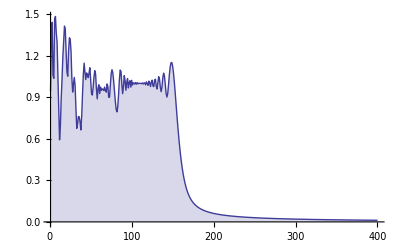

```mathematica
DiscretePlot[Abs[eul2[n,.5+1000I]-Zeta[.5+1000I]],{n,1,400}]
```

```mathematica
ps5a[n_,j_,s_]:=n^(-1/2+s) (1-s) j^-s-n^(1/2-s) s (j^(s-1))
ps5b[n_,j_,s_]:=j^(-1/2)((1-2s)Cosh[(1/2-s)Log[j/n]]+Sinh[(1/2-s)Log[j/n]])
```

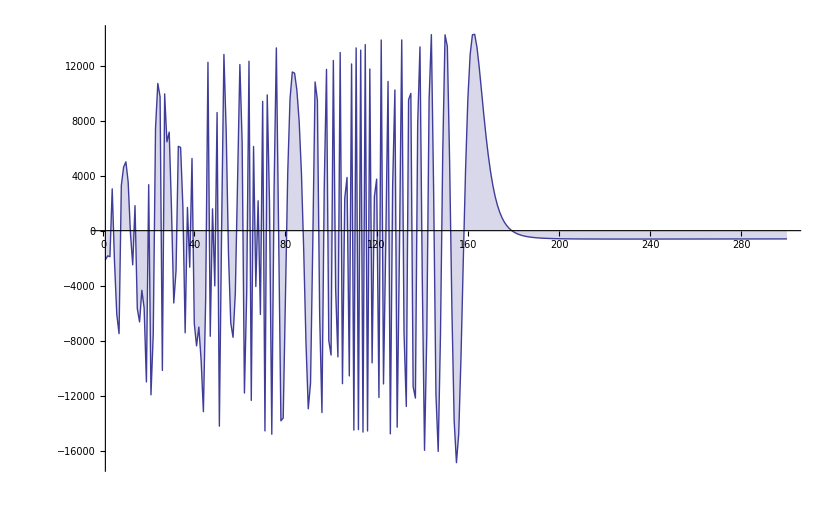

```mathematica
DiscretePlot[Im[ ps8[n,N@ZetaZero@700,.4]],{n,1,300}]
```

```mathematica
fo[n_,s_]:=(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000)
fp[n_,s_]:=n^(1-s)/(1-s)
fp2[n_,s_]:=n^(1-s)/(1-s)+n^-s/2
fp3[n_,s_]:=n^(1-s)/(1-s)+n^-s/2-1/12 n^(-1-s) s
```

```mathematica
fo[100,.5]
```

20.05

```mathematica
(HarmonicNumber[n,s]/fo[n,s]-HarmonicNumber[n,1-s]/fo[n,1-s])/.n->100/.s->.3+2I
```

-0.164126+0.279684 ⅈ

```mathematica
DiscretePlot[{Re@ HarmonicNumber[ n,N@ZetaZero@10], Re@fo[n,N@ZetaZero@10]},{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[{ Re[fo[n,N@ZetaZero@10]]-Re[fp3[n,N@ZetaZero@10]]},{n,1,100}]
```

-Graphics-

```mathematica
N[(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000/.s->ZetaZero@10/.n->10000000]
```

-1.87273×10^-120-2.98119×10^-122 ⅈ

```mathematica
FullSimplify[n^(1/2+t)/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600)]
```

(1209600 n^(1/2+s+t))/(604800-(1209600 n)/(-1+s)-(100800 s)/n+(1680 s (1+s) (2+s))/n^3-(40 s (1+s) (2+s) (3+s) (4+s))/n^5+(s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/n^7)

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
bern[k_]:=If[k==1,1/2,BernoulliB[k]]
bs[n_,s_,t_]:=1/(1-s)Sum[FullSimplify[ bin[1-s,k]bern[k] n^(1-s-k)],{k,0,t}]
bs2[n_,s_,t_]:=FullSimplify[1/(1-s)Sum[FullSimplify[Binomial[1-s,k]bern[k] n^(1-s-k)],{k,0,t}]]
```

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
bern[k_]:=If[k==1,1/2,BernoulliB[k]]
bs[n_,s_,t_]:=1/(1-s)Sum[FullSimplify[ bin[1-s,k]bern[k] n^(1-s-k)],{k,0,t}]
bbs[n_,s_,a_,b_,c_,d_]:=(1-s)^a/s^b Sum[FullSimplify[ bin[s,k]bern[k] n^(c+s-k)],{k,0,d}]/Sum[FullSimplify[ bin[1-s,k]bern[k] n^(c+1-s-k)],{k,0,d}]
```

```mathematica
FullSimplify[n^(c+y)(1-s-y)(s+y)/t^(s+y+1) - n^(c+x)(1-s-x)(s+x)/t^(s+x+1)]
```

n^c t^(-1-s) (n^x t^-x (-1+s+x) (s+x)-n^y t^-y (-1+s+y) (s+y))

```mathematica
n^c t^(-1-s) ((n/t)^x (-1+s+x) (s+x)-(n/t)^y (-1+s+y) (s+y))
```

n^c t^(-1-s) ((n/t)^x (-1+s+x) (s+x)-(n/t)^y (-1+s+y) (s+y))

```mathematica
Integrate[ n^c t^(-1-s) ((n/t)^x (-1+s+x) (s+x)-(n/t)^y (-1+s+y) (s+y)),{t,n,Infinity}]
```

ConditionalExpression[n^(c-s) (x-y),Re[s+x]>0&&Re[s+y]>0&&n>0]

```mathematica
Limit[n^(-.01) (x-y),n->Infinity]
```

0.

```mathematica
Integrate[ n^c t^(-1-s) ((n/t)^x (-1+s+x) (s+x)-(n/t)^y (-1+s+y) (s+y))FractionalPart[t],{t,n,Infinity}]/.x->2/.y->3/.c->2/.s->3
```